## Hrajeme si s Q a LegendreQ...

```mathematica
aQ[n_,m_,z_]=(1-x^2)^Abs[m/2] D[LegendreQ[n,x],{x,Abs[m]}]*Piecewise[{{(-1)^m, m>=0},{(Gamma[n+m+1]/Gamma[n-m+1]),m<0}}]/.x:>z
```

(1-z^2)^(Abs[m]/2) (Piecewise[{{(-1)^Abs[m] (1-z^2)^(-Abs[m]/2) LegendreQ[n,Abs[m],2,z], Abs[m]≥1}, {LegendreQ[n,z], True}}]) (Piecewise[{{(-1)^m, m≥0}, {Gamma[1+m+n]/Gamma[1-m+n], m<0}, {0, True}}])

```mathematica
ath[Infinity,z_]=Piecewise[{{ArcCoth[z],Abs[z]>=1},{ArcTanh[z]-Sign[Im[z]]*I*Pi/2,Abs[z]<1}}];
ath[0,z_]=Piecewise[{{ath[Infinity,z]+I*Pi/2,Im[z]>=0},{ath[Infinity,z]-I*Pi/2,Im[z]<0}}];
ath[1,z_]=Piecewise[{{ath[Infinity,z],Im[z]>=0},{ath[Infinity,z]-I*Pi,Im[z]<0}}];
ath[-1,z_]=Piecewise[{{ath[Infinity,z],Im[z]<0},{ath[Infinity,z]+I*Pi,Im[z]>=0}}];
```

```mathematica
W[n_,z_]:=Sum[LegendreP[k-1,z]LegendreP[n+1-k,z]/k,{k,1,n+1}];
Q[σ_,n_,z_]:=LegendreP[n,z]*ath[σ,z]-W[n-1,z];
```

```mathematica
SQ[σ_,n_,m_,z_]:=Piecewise[{{(-1)^m(1-x^2)^(m/2)D[Q[σ,n,x],{x,m}],m>=0},{(Gamma[n+m+1]/Gamma[n-m+1])(1-x^2)^(-m/2)D[Q[σ,n,x],{x,-m}],m<0}}]/.x:>z;
```

```mathematica
Table[Plot[{LegendreQ[3,n,x],aQ[3,n,x]+0.1,SQ[0,3,n,x]},{x,-2,2}],{n,-2,2}]
```

```mathematica
Table[Q[0,n,x],{n,0,5}]
```

```mathematica
testQ[0,n_,x_]:={Piecewise[{{(ⅈ π)/2+(Piecewise[{{ArcCoth[x], Abs[x]≥1}, {ArcTanh[x]-1/2 ⅈ π Sign[Im[x]], Abs[x]<1}, {0, True}}]), Im[x]≥0}, {-(ⅈ π)/2+(Piecewise[{{ArcCoth[x], Abs[x]≥1}, {ArcTanh[x]-1/2 ⅈ π Sign[Im[x]], Abs[x]<1}, {0, True}}]), Im[x]<0}, {0, True}}],-1+x (Piecewise[{{(ⅈ π)/2+(Piecewise[{{ArcCoth[x], Abs[x]≥1}, {ArcTanh[x]-1/2 ⅈ π Sign[Im[x]], Abs[x]<1}, {0, True}}]), Im[x]≥0}, {-(ⅈ π)/2+(Piecewise[{{ArcCoth[x], Abs[x]≥1}, {ArcTanh[x]-1/2 ⅈ π Sign[Im[x]], Abs[x]<1}, {0, True}}]), Im[x]<0}, {0, True}}]),-(3 x)/2+1/2 (-1+3 x^2) (Piecewise[{{(ⅈ π)/2+(Piecewise[{{ArcCoth[x], Abs[x]≥1}, {ArcTanh[x]-1/2 ⅈ π Sign[Im[x]], Abs[x]<1}, {0, True}}]), Im[x]≥0}, {-(ⅈ π)/2+(Piecewise[{{ArcCoth[x], Abs[x]≥1}, {ArcTanh[x]-1/2 ⅈ π Sign[Im[x]], Abs[x]<1}, {0, True}}]), Im[x]<0}, {0, True}}]),-x^2/2-2/3 (-1+3 x^2)+1/2 (-3 x+5 x^3) (Piecewise[{{(ⅈ π)/2+(Piecewise[{{ArcCoth[x], Abs[x]≥1}, {ArcTanh[x]-1/2 ⅈ π Sign[Im[x]], Abs[x]<1}, {0, True}}]), Im[x]≥0}, {-(ⅈ π)/2+(Piecewise[{{ArcCoth[x], Abs[x]≥1}, {ArcTanh[x]-1/2 ⅈ π Sign[Im[x]], Abs[x]<1}, {0, True}}]), Im[x]<0}, {0, True}}]),-5/12 x (-1+3 x^2)-5/8 (-3 x+5 x^3)+1/8 (3-30 x^2+35 x^4) (Piecewise[{{(ⅈ π)/2+(Piecewise[{{ArcCoth[x], Abs[x]≥1}, {ArcTanh[x]-1/2 ⅈ π Sign[Im[x]], Abs[x]<1}, {0, True}}]), Im[x]≥0}, {-(ⅈ π)/2+(Piecewise[{{ArcCoth[x], Abs[x]≥1}, {ArcTanh[x]-1/2 ⅈ π Sign[Im[x]], Abs[x]<1}, {0, True}}]), Im[x]<0}, {0, True}}]),-1/12 (-1+3 x^2)^2-3/8 x (-3 x+5 x^3)-3/20 (3-30 x^2+35 x^4)+1/8 (15 x-70 x^3+63 x^5) (Piecewise[{{(ⅈ π)/2+(Piecewise[{{ArcCoth[x], Abs[x]≥1}, {ArcTanh[x]-1/2 ⅈ π Sign[Im[x]], Abs[x]<1}, {0, True}}]), Im[x]≥0}, {-(ⅈ π)/2+(Piecewise[{{ArcCoth[x], Abs[x]≥1}, {ArcTanh[x]-1/2 ⅈ π Sign[Im[x]], Abs[x]<1}, {0, True}}]), Im[x]<0}, {0, True}}])}[[n+1]]
```

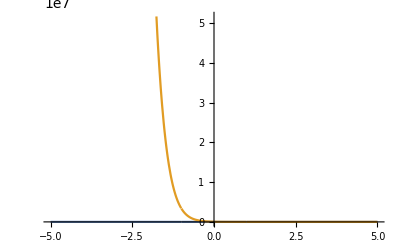

```mathematica
Plot[{Re[Q[0,1,I x]+0.1],Re[newq[1,7,6,x]]},{x,-5,5}]
```

## Hrajeme si podruhé

```mathematica
newQ[0,n_,m_,z_]:=LegendreQ[n,m,z]
```

```mathematica
newQ[σ_,n_,m_,z_]:=newQ[0,n,m,z]+Piecewise[{{-(ⅈ π)/2 LegendreP[n,m,z],σ>0},{(ⅈ π)/2 LegendreP[n,m,z],σ<0}},0]
```

```mathematica
Definition[newQ]
```

newQ[0,n_,m_,z_]:=LegendreQ[n,m,z]
 
newQ[σ_,n_,m_,z_]:=newQ[0,n,m,z]+(Piecewise[{{1/2 (-(ⅈ π)) LegendreP[m,n,z], σ>0}, {1/2 (ⅈ π) LegendreP[m,n,z], σ<0}, {0, True}}])

```mathematica
newq[σ_,n_,m_,z_]:=(-I)^(1+m+n)newQ[σ,n,m,I*z]
```